## Оптимизация

### Встроенные функции вместо написанных самому

```mathematica
(*перестановка элементов в списке*)
```

```mathematica
mat={{a,b},{c,d},{d,e}};
```

```mathematica
temp=ConstantArray[0,{Length[mat]}];
```

```mathematica
Do[temp[[i]]={mat⟦i,2⟧,mat⟦i,1⟧},{i,1,Length[mat]}];
```

```mathematica
temp
```

{{b,a},{d,c},{e,d}}

```mathematica
(*встроенная функция*)
```

```mathematica
Map[Reverse,mat] (*более компактно и работает быстрее*)
```

{{b,a},{d,c},{e,d}}

```mathematica
mat=RandomReal[1,{10^6,2}];
```

```mathematica
Timing[temp=ConstantArray[0,{Length[mat]}];Do[temp[[i]]={mat⟦i,2⟧,mat⟦i,1⟧},{i,1,Length[mat]}]]
```

{1.14063,Null}

```mathematica
AbsoluteTiming[Map[Reverse,mat];]
```

{0.0644714,Null}

```mathematica
(*суммирование элементов списка*)
```

```mathematica
sumDo[n_]:=Module[{i=0,result=0},Do[result=result+i,{i,1.0,n}];
result]
```

```mathematica
Timing[sumDo[10^6]]
```

{0.3125,5.00001×10^11}

```mathematica
sumTable[n_]:=Module[{result=0.0},Table[result=result+i,{i,1.0,n}];result]
```

```mathematica
Timing[sumTable[10^6]]
```

{0.34375,5.00001×10^11}

```mathematica
sumApply[n_]:=Apply[Plus,N@Range[n]]
```

```mathematica
Timing[sumApply[10^6]]
```

{0.109375,5.00001×10^11}

```mathematica
sumTotal[n_]:=Total[N@Range[n]] (*самый быстрый способ*)
```

```mathematica
Timing[sumTotal[10^6]]
```

{0.,5.00001×10^11}

```mathematica
Timing[Sum[i,{i,1.0,10^6}]]  (*медленее Total , т.к. может суммировать не только числа*)
```

{0.109375,5.00001×10^11}

```mathematica
(*немного математики*)
```

```mathematica
Binomial[10^6+1,2]//Timing
```

{0.,500000500000}

```mathematica
Binomial[10^6+1,2] ==Total[Range[10^6]]
```

True

### Pattern matching

```mathematica
(*считает положительные элементы списка*)
```

```mathematica
vec=RandomReal[{-1,1},{15}]
```

{0.226246,-0.632279,-0.371866,0.766558,-0.409341,-0.922516,0.145589,0.499644,0.664885,0.787178,0.038372,-0.668142,0.748044,0.319893,-0.618139}

```mathematica
Count[vec,_?Positive]
```

9

```mathematica
Sign[vec]
Sign[vec]+1
Total[Sign[vec]+1]/2
```

{1,-1,-1,1,-1,-1,1,1,1,1,1,-1,1,1,-1}

{2,0,0,2,0,0,2,2,2,2,2,0,2,2,0}

9

```mathematica
vec=RandomReal[{-1,1},{10^6}];
Count[vec,_?Positive]//Timing
```

{0.25,500565}

```mathematica
Total[Sign[vec]+1]/2//Timing (*Total и Sign работают только с числами*)
```

{0.,500565}

```mathematica
(*построение верхне треугольной матрицы*)
```

```mathematica
With[{n=5},SparseArray[{i_,j_}/;i≤j->1,{n,n}]]//MatrixForm
```

(1 | 1 | 1 | 1 | 1
0 | 1 | 1 | 1 | 1
0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1)

```mathematica
With[{n=500},matSA=SparseArray[{i_,j_}/;i≤j->1,{n,n}]]//Timing (*проверка и сравнение с паттерном каждый раз*)
```

{0.15625,SparseArray[<125250>, {500, 500}]}

```mathematica
With[{n=500},matT=Table[If[j≥i,1,0],{i,n},{j,n}];]//Timing
```

{0.,Null}

```mathematica
matT=Table[0,{i,10^4},{j,10^4}];//Timing
```

{0.625,Null}

```mathematica
matSA=SparseArray[{_,_}->0,{10^4,10^4}];//Timing (*одно правило для всех элементов матрицы, результат лучше чем у Table*)
```

{0.,Null}

```mathematica
{matSA==matT,matSA===matT} (*разные структуры у матриц*)
```

{True,False}

### Уменьшение числа вычислений

```mathematica
(*складываем числа до 10^6*)
```

```mathematica
(For[i=0;result=0,i≤10^6,i++,result=result+i];
result)//Timing (*слишком много промежуточных вычислений на каждом шаге*)
```

{0.765625,500000500000}

```mathematica
(result=0;
Do[result=result+i,{i,1,10^6}];
result)//Timing
```

{0.3125,500000500000}

```mathematica
(*The Sieve of Eratosthenes со счетчиком числа вычислений*)
```

```mathematica
SieveCnt[n_Integer]:=Module[{ints=Range[n],p,cnt=0},For[p=2,p≠1&&p≤Floor[Sqrt[n]],p++,Do[ints[[i]]=1;cnt++,{i,2 p,n,p}]];
DeleteCases[ints,1];
cnt]
```

```mathematica
SieveCnt[10^5]//Timing
```

{0.4375,532988}

```mathematica
Sieve2[n_Integer]:=Module[{ints=Range[n]},Do[ints[[2 p;; -1;;p]]=1,{p,2,√n}];DeleteCases[ints,1]] (*переписали функцию по-новому*)
```

```mathematica
Sieve2[100]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

```mathematica
{Length[Sieve2[1000]],PrimePi[1000]}
```

{168,168}

```mathematica
Sieve2[10^5];//Timing
```

{0.015625,Null}

```mathematica
Sieve2Cnt[n_Integer]:=Module[{ints=Range[n],cnt=0},Do[ints[[2 p;;-1;;p]]=1;
cnt++,{p,2,√n}];
DeleteCases[ints,1];
cnt] (*поставили счетчик числа вычислений*)
```

```mathematica
Sieve2Cnt[10^5]//Timing
```

{0.,315}

### Listability Списочность

```mathematica
{1,2,3,4}+{10,20,30,40}
```

{11,22,33,44}

```mathematica
vec=RandomReal[{-100,100},10^6];
```

```mathematica
AbsoluteTiming[Map[Sin,vec];]
```

{0.0438299,Null}

```mathematica
AbsoluteTiming[Sin[vec];]
```

{0.0030664,Null}

```mathematica
f[x_]:=If[-1<x<1,Exp[x],x^2]
```

```mathematica
pureF=Function[{x},If[11<x<1,Exp[x],x^2],Listable];
```

```mathematica
{AbsoluteTiming[Map[f,vec];],AbsoluteTiming[pureF[vec];]}
```

{{0.981074,Null},{0.0721798,Null}}

### Packed arrays

```mathematica
mat=RandomReal[1,{1000,1000}]; (*автоматическая упаковка, т.к. все элементы числа*)
```

```mathematica
Developer`PackedArrayQ[mat]
```

True

```mathematica
matUnp=ReplacePart[mat,1,{1,2}]; (*не упакованный массив чисел *)
```

```mathematica
Developer`PackedArrayQ[matUnp]
```

False

```mathematica
Map[ByteCount,{mat,matUnp}] (*памяти на хранение*)
```

{8000208,24200192}

```mathematica
Timing[Do[mat+Transpose[mat],{100}];] (*сравним время работы *)
```

{0.1875,Null}

```mathematica
Timing[Do[matUnp+Transpose[matUnp],{100}];]
```

{5.42188,Null}

```mathematica
vec=RandomReal[{-1,1},{10^6}]; (*вернемся к примеру с паттерными*)
```

```mathematica
Count[vec,_?Positive]//Timing (*count распаковывает массив*)
```

{0.25,499690}

```mathematica
On["Packing"] (*сообщение, если распаковывается массив*)
```

```mathematica
Count[vec,_?Positive]
```

Developer`FromPackedArray::unpack: Unpacking array in call to Count.

499690

```mathematica
Total[Sign[vec]+1]/2
```

499690

```mathematica
Off["Packing"] (*выключили выдачу сообщений*)
```

```mathematica
m1=Table[i^2,{i,1.0,249}];m2=Table[i^2,{i,1.0,250}]; (*упаковывать массив имеет смысл, если он достаточно большой. Для Table достаточно это 250 элементов*)
```

```mathematica
{Developer`PackedArrayQ[m1],Developer`PackedArrayQ[m2]}
```

{False,True}

```mathematica
SystemOptions["CompileOptions"];
```

```mathematica
(*случайные блуждания*)
```

```mathematica
NSEW={{0,1},{0, -1},{1,0},{-1,0}}; (*не упакованный массив*)
```

```mathematica
{Developer`PackedArrayQ[NSEW],Developer`PackedArrayQ[RandomChoice[NSEW,{10}]]}
```

{False,True}

```mathematica
nsewPacked=Developer`ToPackedArray[NSEW] (*принудительно упаковали*)
```

{{0,1},{0,-1},{1,0},{-1,0}}

```mathematica
{Developer`PackedArrayQ[nsewPacked],Developer`PackedArrayQ[RandomChoice[nsewPacked,{100}]]}
```

{True,True}

```mathematica
(*сравним скорость работы*)
```

```mathematica
walk2D[n_]:=Accumulate[RandomChoice[NSEW,{n}]]
```

```mathematica
walk2DPacked[n_]:=Accumulate[RandomChoice[nsewPacked,{n}]]
```

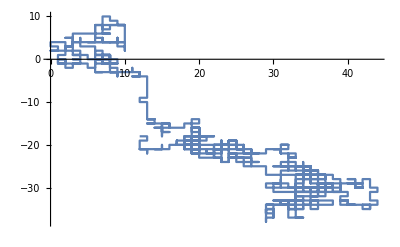
{-Graphics-,-Graphics-}

```mathematica
With[{steps=1000},{SeedRandom[0];ListLinePlot[walk2D[steps]],SeedRandom[0];ListLinePlot[walk2DPacked[steps]]}]
```

```mathematica
{AbsoluteTiming[w=walk2D[10^7];],AbsoluteTiming[wP=walk2DPacked[10^7];]}
```

{{0.223208,Null},{0.239793,Null}}

```mathematica
{ByteCount[w],ByteCount[wP]}
```

{160000208,160000208}

```mathematica
(*преимущество при задании функции, как чистой, тоже начинает работать с достаточного большого объема данных*)
```

```mathematica
funP=Function[{x},x^2+1];
```

```mathematica
fun[x_]:=x^2+1;
```

```mathematica
vec=RandomReal[{-100,100},10^6];
```

```mathematica
{AbsoluteTiming[Map[funP,vec];],AbsoluteTiming[Map[fun,vec];]}
```

{{0.0397622,Null},{0.729361,Null}}

```mathematica
vecSmall=RandomReal[{-100,100},{99}]; (*для вектора маленькой длины разница в скорости не так заметна*)
```

```mathematica
{AbsoluteTiming[Map[funP,vecSmall];],AbsoluteTiming[Map[fun,vecSmall];]}
```

{{0.000112,Null},{0.0000958,Null}}

## Parallel Mathematica

```mathematica
ints={6816621442891306800904744383119905653635103 851,73388383728563244425930590337481080121879717077,52013328811529395666589446962910372930994642737,505513202541467917512749204086148326575935117323};
```

```mathematica
AbsoluteTiming[Map[FactorInteger,ints]]
```

{3.021597,{{{3,1},{23,1},{37,1},{73,1},{83,1},{997,1},{376141983903589891692171987333508787,1}},{{2294373045611351,1},{3323461128609971,1},{9624378352212737,1}},{{1570432314085519,1},{5086852194050141,1},{6510979192425803,1}},{{7415796267244853,1},{7673045464769561,1},{8883967089924631,1}}}}

```mathematica
$ProcessorCount
```

4

```mathematica
LaunchKernels[]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
ParallelEvaluate[$ProcessID]
```

{15796,17380,17500,15424}

```mathematica
ParallelEvaluate[$MachineName]
```

{eva-x1carbon-8,eva-x1carbon-8,eva-x1carbon-8,eva-x1carbon-8}

```mathematica
AbsoluteTiming[ParallelMap[FactorInteger,ints]]
```

{1.49977,{{{3,1},{23,1},{37,1},{73,1},{83,1},{997,1},{376141983903589891692171987333508787,1}},{{2294373045611351,1},{3323461128609971,1},{9624378352212737,1}},{{1570432314085519,1},{5086852194050141,1},{6510979192425803,1}},{{7415796267244853,1},{7673045464769561,1},{8883967089924631,1}}}}

```mathematica
Select[Table[2^Prime[n]-1,{n,1,1000}],PrimeQ];//
AbsoluteTiming
```

{30.2775,Null}

```mathematica
Parallelize[Select[Table[2^Prime[n]-1,{n,1,1000}],PrimeQ]];//
AbsoluteTiming
```

{12.2816,Null}

```mathematica
Parallelize[Accumulate[Range[40]]]
```

Parallelize::nopar1: Accumulate[Range[40]] cannot be parallelized; proceeding with sequential evaluation.

{1,3,6,10,15,21,28,36,45,55,66,78,91,105,120,136,153,171,190,210,231,253,276,300,325,351,378,406,435,465,496,528,561,595,630,666,703,741,780,820}

```mathematica
(*некоторые встроенные функции автоматически распараллеливают вычисления*)
```

```mathematica
vec=RandomReal[1,10^7];
```

```mathematica
Do[Total[vec],{100}]//AbsoluteTiming
```

{0.333184,Null}

```mathematica
ParallelDo[Total[vec],{100}]//AbsoluteTiming
```

{0.628887,Null}

```mathematica
mat=RandomReal[1,{500,500}];
```

```mathematica
Do[Inverse[mat],{100}]//AbsoluteTiming
```

{0.500554,Null}

```mathematica
ParallelDo[Inverse[mat],{100}]//AbsoluteTiming
```

{0.331821,Null}

edit->preferences

```mathematica
SystemInformation[]
```

1234567

```mathematica
TableForm[ParallelEvaluate[{$KernelID,$MachineName,$SystemID,$VersionNumber,$ProcessID,TimeUsed[], MaxMemoryUsed[],"ProcessPriority"/.SystemOptions["ProcessPriority"]}],TableHeadings->{None,{"ID","host", "OS","Version", "Process","CPU Time","Memory", "Priority"}},TableDepth->2]
```

ID | host | OS | Version | Process | CPU Time | Memory | Priority
1 | eva-x1carbon-8 | Windows-x86-64 | 12.1 | 15796 | 14.344 | 144725848 | BelowNormal
2 | eva-x1carbon-8 | Windows-x86-64 | 12.1 | 17380 | 13.704 | 144762704 | BelowNormal
3 | eva-x1carbon-8 | Windows-x86-64 | 12.1 | 17500 | 11.657 | 144726744 | BelowNormal
4 | eva-x1carbon-8 | Windows-x86-64 | 12.1 | 15424 | 9.75 | 144761688 | BelowNormal

генерируем случайные числа

```mathematica
Take[{a,b,c,d,e,f},4]
```

{a,b,c,d}

```mathematica
RandomInteger[{-100,100},4]
```

{-39,25,97,87}

```mathematica
Take[Flatten[ParallelEvaluate[RandomInteger[{-100,100},Ceiling[100/$KernelCount]]]],100]
```

{-94,-21,84,91,-76,82,-7,42,-45,9,46,-86,34,-6,65,-21,-54,74,-47,65,-54,-12,-17,-76,-78,-72,-100,48,74,26,8,78,-63,-58,90,-79,36,93,-86,-69,99,-16,-95,59,-31,45,-16,-27,53,97,91,-55,-51,-17,12,-37,-34,-28,-13,-94,81,53,-56,29,-86,40,8,15,-64,-97,-2,73,-44,-5,-69,17,53,-35,-38,-50,87,-75,55,-20,32,-96,29,-63,15,-24,-96,-100,-25,5,-88,-22,-97,96,-62,97}

```mathematica
vars=With[{num=1001},Take[Flatten[ParallelEvaluate[RandomInteger[{-100,100},Ceiling[num/$KernelCount]]]],num]];Length[vars]
```

1001

```mathematica
ParallelEvaluate[Sin[π/3]] (*считаем везде*)
```

{(√3)/2,(√3)/2,(√3)/2,(√3)/2}

```mathematica
Kernels[]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
firstKernel=Kernels[][[1]];
```

```mathematica
ParallelEvaluate[Sin[π/3],firstKernel]
```

(√3)/2

```mathematica
ParallelEvaluate[{$KernelID,$ProcessID}]
```

{{1,15796},{2,17380},{3,17500},{4,15424}}

```mathematica
semiPrimes=Apply[Times,Map[Prime,RandomInteger[{10000,100000},{1000,2}]],{1}];
```

```mathematica
Map[Prime,RandomInteger[{1,10},{3,2}]]
Apply[Times,%,{1}]
```

{{23,29},{11,29},{5,23}}

{667,319,115}

```mathematica
Map[FactorInteger,semiPrimes]
```

{{{622943,1},{951079,1}},{{187081,1},{717679,1}},{{184703,1},{904577,1}},995,{{250109,1},{913483,1}},{{290761,1},{963323,1}}}
 |  |  |  |

```mathematica
{t1,res1}=AbsoluteTiming[Map[FactorInteger,semiPrimes];]
{t2,res2}=AbsoluteTiming[Parallelize[Map[FactorInteger,semiPrimes]];]
t1/t2
```

{0.338209,Null}

{0.226259,Null}

1.49478

```mathematica
fmaxFactor[x_Integer]:=Max[Power@@@FactorInteger[x]]
```

```mathematica
fmaxFactor[1000]
```

125

```mathematica
FactorInteger[1000]
Apply[Power,%,{1}]
Max[%]
```

{{2,3},{5,3}}

{8,125}

125

```mathematica
DistributeDefinitions[fmaxFactor]
Parallelize[Map[fmaxFactor,semiPrimes]]//Short
```

{fmaxFactor}

{951079,717679,«996»,913483,963323}

```mathematica
{timing1,result}= AbsoluteTiming[Parallelize[
Map[FactorInteger,semiPrimes],Method -> "CoarsestGrained"]];timing1
```

0.128972

```mathematica
{timing2,result}= AbsoluteTiming[Parallelize[
Map[FactorInteger,semiPrimes],Method -> "FinestGrained"]];timing2
```

0.389255

```mathematica
integersList=RandomInteger[{0,10^8},10000000];
ParallelCombine[Total,integersList,Plus]
```

500245974637837

ParallelMap

```mathematica
ParallelMap[PrimeOmega,RandomInteger[{10^40,10^50},32]]
```

{5,3,8,3,5,5,5,8,5,4,5,7,5,9,7,7,4,14,10,6,6,9,10,4,9,4,8,2,6,4,6,6}

```mathematica
PrimeOmega[2^2 3^7]
```

9

```mathematica
Module[{data=RandomInteger[{10^4,10^5},3]},SeedRandom[8];
Column[{
AbsoluteTiming[ParallelMap[PrimeOmega,data]],AbsoluteTiming[Map[PrimeOmega,data]]}]]
```

{0.00193,{1,3,2}}
{0.000073,{1,3,2}}

Mandelbrot Fractal

Here the Mandelbrot has only the boundaries as parameters.

Mandelbrot[{y0 , y1,  dy},{x0 ,x1 , dx}]

```mathematica
NextStep[a_,b_][{x_,y_,n_}]=
	If[ x^2+y^2  >4 || n>20 
		,Throw[Sqrt[x^2+y^2]],{x^2-y^2+a,2*x*y+b,n+1}]//N;

Mandelbrot[{x0_,x1_,dx_},{y0_,y1_,dy_}]:= Module[{Mat},
Mat =Table[
 Catch[FixedPoint[NextStep[a,b], {0,0,0} ]]
           ,{a,x0,x1,dx},{b,y0,y1,dy}];
Map[ If[#>2,1,0]&, Mat ,{2} ]		
	]
```

```mathematica
ListDensityPlot[
Mandelbrot[{-2,0.6,0.01},{-1,1,0.01}]
,Mesh->False,AspectRatio->Automatic]
```

-Graphics-

```mathematica
Clear[mbrotColor]
mbrotColor[c_Complex]:=Module[{max =10, r},
r =NestWhile[{#⟦1⟧+1, #⟦2⟧^2 +c}&,
{0, c}, Norm[#⟦2⟧]<2 &, 1, max]⟦1⟧;
1.0 -((max -r)/max)^2]
DistributeDefinitions[mbrotColor]
With[{granularity =0.004},
ArrayPlot[Transpose[ParallelTable[mbrotColor[i +j I],
{i, -2, 0.75, granularity},
{j, -1, 1, granularity}]], ImageSize ->450]]
```

{mbrotColor}

-Graphics-

```mathematica
images=ParallelTable[
SphericalPlot3D[If[θ<Pi/4,None,1/(ϕ+5)],{θ,0,Pi},{ϕ,0,i Pi},PlotStyle ->Directive[Orange,Specularity[White,10]],Mesh ->None,PlotPoints ->30,Axes ->None,Boxed ->False],{i,1,8,0.25}];
ListAnimate[images,ImageSize ->Small]
```

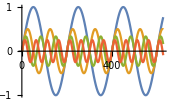

```mathematica
ListLinePlot[ParallelTable[Sin[n Pi x]/n,{n,1,4},{x,0,2 Pi,0.01}]]
```

## Packages

```mathematica
<<StatisticalPlots` (*подключаем пакет*)
```

```mathematica
Needs["StatisticalPlots`"] (* или так *)
```

```mathematica
?StatisticalPlots`ParetoPlot
```

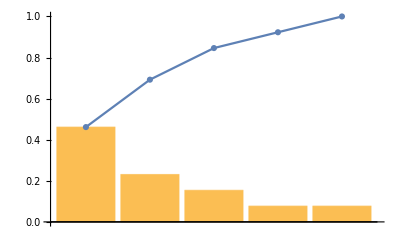

```mathematica
data={v,u,y,w,w,u,u,z,v,u,v,u,u};
ParetoPlot[data]
```

```mathematica
Names["StatisticalPlots`*"] (*функции из пакета*)
```

{BoxExtraSpacing,BoxFillingStyle,BoxLabels,BoxLineStyle,BoxMedianStyle,BoxOrientation,BoxOutlierMarkers,BoxOutliers,BoxQuantile,BoxWhiskerPlot,ColumnLabels,DataLabels,DataRanges,DataSpacing,DataTicks,IncludeEmptyStems,IncludeStemCounts,IncludeStemUnits,Leaves,PairwiseScatterPlot,ParetoPlot,PlotDirection,StemExponent,StemLeafPlot}